```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["output.wl"];
data["config","resultColumns"]
cols=AssociationThread[data["config","resultColumns"]->Range[Length[data["config","resultColumns"]]]];
results=data["results"];
```

{targetScore,lambda,weightedExpectedCost,successProbability,echoPerSuccess,tunerPerSuccess,expPerSuccess}

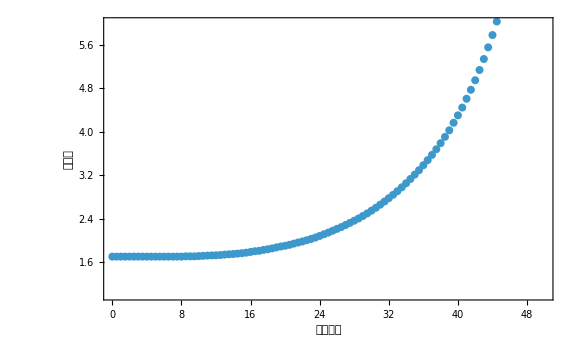

```mathematica
ListPlot[results[[All,{cols["targetScore"],cols["tunerPerSuccess"]}]],Frame->True,FrameLabel->{"目标分数","调谐器"},ScalingFunctions->{"Linear","Log10"},PlotRange->{{0,50},{10,10^6}},ImageSize->Large,FrameStyle->Directive[Black,AbsoluteThickness[1.0]],LabelStyle->Directive[FontFamily->"Helvetica",15],FrameTicksStyle->Directive[Black,15],PlotStyle->Directive[PointSize[0.01]],ImagePadding->{{70,40},{50,20}}]
```

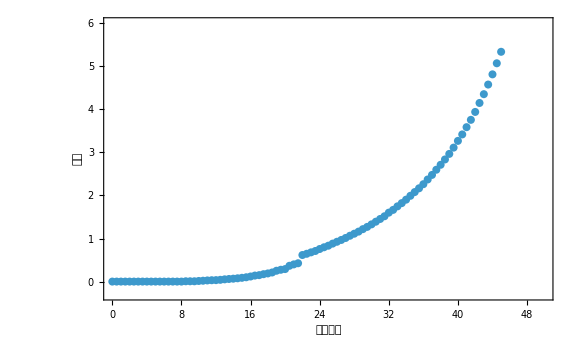

```mathematica
ListPlot[results[[All,{cols["targetScore"],cols["echoPerSuccess"]}]],Frame->True,FrameLabel->{"目标分数","胚子"},ScalingFunctions->{"Linear","Log10"},PlotRange->{{0,50},{0.5,10^6}},ImageSize->Large,FrameStyle->Directive[Black,AbsoluteThickness[1.0]],LabelStyle->Directive[FontFamily->"Helvetica",15],FrameTicksStyle->Directive[Black,15],PlotStyle->Directive[PointSize[0.01]],ImagePadding->{{70,40},{50,20}}]
```